# Mathematica III - Linear Algebra

## Based on Labs developed by John S. Colton, BYU Physics & Astronomy, based in part on past labs by Branton Cambell and Steve Turley

In most fields of science and engineering, the easiest multi-variable problems are the "linear" ones, where the unknown quantities appear in linear combinations with constant coefficients.  Linear problems are usually solved by straightforward methods and have exact solutions.  Non-linear problems, on the other hand, can become very difficult very quickly.  In this lab, we will explore matrix and vector properties and operations, practice formulating problems in terms of matrix/vector equations, and learn how to use Mathematica's linear-algebra capabilities to solve simple and moderately-challenging math and physics problems.

```mathematica
Clear["`*" ]
```

## Lists & vectors

Lists are Mathematica objects that are items grouped together with curly brackets. A list can be any collection of items: numbers, unassigned variables, plots, even other lists.  You' ve already used them in a few ways--to specify limits in the Plot command, to apply a list of rules inside functions, and to evaluate functions with variables set to particular values.  In addition to their utility in evaluating functions, the three primary purposes of lists are to (1) serve as “arrays” for programming purposes, (2) allow you to do linear algebra with vectors and matrices, and (3) allow you to manipulate real data.  We’ll focus on #2 here.

### How to create a list.

There are numerous ways to create lists in Mathematica. Look over these examples and press F1 on the function names if it’s not clear what’s going on.

```mathematica
list = {1,2,3,4,5}
```

{1,2,3,4,5}

```mathematica
list^2
```

{1,4,9,16,25}

```mathematica
list2={a,b,c,d,e}
```

{a,b,c,d,e}

```mathematica
list2^2
```

{a^2,b^2,c^2,d^2,e^2}

```mathematica
(#^2 &) @list   (* nameless function to operate on list elements, prefix form *)
```

{1,4,9,16,25}

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Range[10,20]
```

{10,11,12,13,14,15,16,17,18,19,20}

```mathematica
range = Range[0,10,.2]    (* general format for Range:  start, end, step size *)
```

{0.,0.2,0.4,0.6,0.8,1.,1.2,1.4,1.6,1.8,2.,2.2,2.4,2.6,2.8,3.,3.2,3.4,3.6,3.8,4.,4.2,4.4,4.6,4.8,5.,5.2,5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.}

```mathematica
(#^2 &) @ range
```

{0.,0.04,0.16,0.36,0.64,1.,1.44,1.96,2.56,3.24,4.,4.84,5.76,6.76,7.84,9.,10.24,11.56,12.96,14.44,16.,17.64,19.36,21.16,23.04,25.,27.04,29.16,31.36,33.64,36.,38.44,40.96,43.56,46.24,49.,51.84,54.76,57.76,60.84,64.,67.24,70.56,73.96,77.44,81.,84.64,88.36,92.16,96.04,100.}

```mathematica
Table[n^2, {n,3,7}]
```

{9,16,25,36,49}

```mathematica
Table[n^2, {n,1,5,0.1}]    (* general format for Table: start, end, step size  *)
```

{1.,1.21,1.44,1.69,1.96,2.25,2.56,2.89,3.24,3.61,4.,4.41,4.84,5.29,5.76,6.25,6.76,7.29,7.84,8.41,9.,9.61,10.24,10.89,11.56,12.25,12.96,13.69,14.44,15.21,16.,16.81,17.64,18.49,19.36,20.25,21.16,22.09,23.04,24.01,25.}

```mathematica
f[x_] = x^3;
Array[f, 10]
```

{1,8,27,64,125,216,343,512,729,1000}

```mathematica
Array[#^3&,10]
```

{1,8,27,64,125,216,343,512,729,1000}

Things to observe: There are lots of ways to construct lists! The five ways used here are:
1. Manually defining a list with curly brackets.
2. Operating on an existing list
3. The Range command, to create an equally-spaced set of “points” (list elements)
4. The Table command, as a very flexible way of creating a set of function values
5. The Array command, as a slightly less flexible way of doing the same (with some added capability to create multi-dimensional lists)

### “Regular vectors” are lists

Here’s an example of a vector

```mathematica
vec={1,2,3}
```

{1,2,3}

## Defining matrices

### Typing in matrix elements and viewing matrices in standard form

A matrix is a list of lists.  Each of the sub-lists is a list of row elements.  One way to enter them is to type them in directly.

```mathematica
matx1={{1,2,3},{4,5,7},{8,9,10}} 
matx2={{11},{12},{13}}
matx3={{14, 15, 16}}
```

{{1,2,3},{4,5,7},{8,9,10}}

```mathematica
{{11},{12},{13}}
```

{{11},{12},{13}}

You can view them in standard matrix form using MatrixForm:

```mathematica
MatrixForm[matx1]
matx2//MatrixForm  (*using postfix notation - often easier!*)
matx3//MatrixForm
```

(1 | 2 | 3
4 | 5 | 7
8 | 9 | 10)

(11
12
13)

(14 | 15 | 16)

The MatrixForm command works on regular vectors too:

```mathematica
vec
vec//MatrixForm
```

{1,2,3}

(1
2
3)

IMPORTANT: Be careful that, when you define matrices (or vectors), you do not include MatrixForm in the definition - just use it after the definition to view them.  For example:

```mathematica
incorrect={{a,b},{c,d}}   //MatrixForm  (* this will produce bad results *)
incorrect //Det  (* The determinant function fails to work *)

correct={{a,b},{c,d}}  
% //MatrixForm  
correct //Det (* this works! *)
```

(a | b
c | d)

Det[(a | b
c | d)]

{{a,b},{c,d}}

(a | b
c | d)

-b c+a d

The “incorrect” example doesn’t work because the formatting statement MatrixForm has been included as part of the definition, which prevents it from behaving as a matrix.

### Two ways to use templates to enter matrices

You can also use templates to insert matrices.  
Method #1:  From the toolbar at the top of the screen, choose Palettes, Basic Math Assistant.  Under “Basic Commands” open the matrix tab: 
 -Graphics-
Here you’ll find a matrix template, and lots of typical matrix commands.

Method #2: In addition, you can insert matrices using Insert...Table/Matrix from the toolbar at the top of the screen: -Graphics-

There are lots of other ways to generate matrices - from data, from functions, etc.  See the tutorial howto/CreateAMatrix

### Problem 1: Matrices three ways

a) Create three 3x2 matrices (3 rows, 2 columns) and name them M1, M2, and M3 in the following ways: 
 (1) Create M1 by typing in entries directly as a list of lists.  
 
 (2) Use the Palette to create M2.  
 (3) Use Insert...Table/Matrix to create M3.  Use whatever values you like but make each matrix different.  Make use of these keyboard shortcuts:

For the template-created matrices, use the keyboard commands
	Tab or arrow	to move through the empty placeholders
	Ctrl-Enter	to enter a new row immediately below the cursor
	Ctrl-,		to enter a new column to the right of the cursor
	Ctrl-Space	to move out of the matrix
You can also start a new matrix simply by typing Ctr-Enter or Ctrl-,

b) Enter each matrix name to evaluate it and verify that it is a list of lists, regardless of the entry method

c) On another line use MatrixForm to view each matrix in standard format

```mathematica
(*a*)
M1 = {{w,u},{v,x},{y,z}}
```

{{w,u},{v,x},{y,z}}

```mathematica
M2 = ({{6, 7}, {7, 8}, {8, 9}})
```

{{6,7},{7,8},{8,9}}

```mathematica
M3 = ({{-1, -2}, {2, 7}, {-4, -5}})
```

{{-1,-2},{2,7},{-4,-5}}

```mathematica
(*b*)
M1
M2
M3
```

{{w,u},{v,x},{y,z}}

{{6,7},{7,8},{8,9}}

{{-1,-2},{2,7},{-4,-5}}

```mathematica
(*c*)
M1 //MatrixForm
M2 //MatrixForm
M3 //MatrixForm
```

(w | u
v | x
y | z)

(6 | 7
7 | 8
8 | 9)

(-1 | -2
2 | 7
-4 | -5)

### 1D matrices vs “regular” vectors

It may seem like one-dimensional matrices are the same as vectors, but that’s not quite true.  Evaluate the examples below, which contain a “regular vector” v, and the 3x1 and 1x3 matrices A and B, respectively. Elements like A and B are often called “column vectors” and “row vectors”, but Mathematica treats them a little differently than just “regular vectors” such as {1,2,3}. Specifically, these column and row vectors are 2D matrices whereas a regular vector is a 1D list of three elements, and you don’t have to specify whether it is a row or column vector. Most of the time Mathematica will figure out how to handle a “regular vector” as shown in the multiplication examples which follow.

```mathematica
v={1,2,3}; (* regular vector *)
A = {{4},{5},{6}};  (* 3x1 column matrix *)
B = {{7,8,9}};  (* 1x3 row matrix *)
matx4={{a,b,c},{d,e,f}}; (* a 2x3 matrix to test out the vectors on *)
matx5={{a,b},{c,d},{e,f}}; (* a 3x2 matrix to test out the vectors on *)
MatrixForm/@{v,A,B,matx4,matx5} (* the command MatrixForm "mapped" onto A, B, v, and matx4 *)
```

{(1
2
3),(4
5
6),(7 | 8 | 9),(a | b | c
d | e | f),(a | b
c | d
e | f)}

```mathematica
matx4.v//MatrixForm (* the product ({{a, b, c}, {d, e, f}})({{1}, {2}, {3}}) Mathematica treats the vector v as a column vector*)
matx4.A//MatrixForm(* the product ({{a, b, c}, {d, e, f}})({{4}, {5}, {6}}) *)
matx4.B//MatrixForm (* the product ({{a, b, c}, {d, e, f}})({{7, 8, 9}}) which does NOT work *)
```

(a+2 b+3 c
d+2 e+3 f)

(4 a+5 b+6 c
4 d+5 e+6 f)

Dot::dotsh: Tensors {{a,b,c},{d,e,f}} and {{7,8,9}} have incompatible shapes.

{{a,b,c},{d,e,f}}.{{7,8,9}}

```mathematica
v.matx5//MatrixForm (* the product ({{1, 2, 3}})({{a, b}, {c, d}, {e, f}}) Mathematica treats the vector v as a row vector*)
A.matx5//MatrixForm(* the product ({{4}, {5}, {6}})({{a, b}, {c, d}, {e, f}}) which does NOT work *)
B.matx5//MatrixForm (* the product ({{7, 8, 9}})({{a, b}, {c, d}, {e, f}}) *)
```

(a+2 c+3 e
b+2 d+3 f)

Dot::dotsh: Tensors {{4},{5},{6}} and {{a,b},{c,d},{e,f}} have incompatible shapes.

{{4},{5},{6}}.{{a,b},{c,d},{e,f}}

(7 a+8 c+9 e | 7 b+8 d+9 f)

### How to access individual matrix elements / vector components

Mathematica uses double square brackets to indicate specific list elements. (This is technically a shortcut for the Part function.) For example:

```mathematica
vec={1,2,3}
vec[[3]]
```

```mathematica
vec[3] (*wrong way!)
```

Things to observe:
1. If you accidentally try to access a list element using single square brackets instead of double, Mathematica will be very confused. In the example labeled “wrong way”, it thinks that you want to evaluate the vec function at x=3. But no such function exists, so it is unable to comply with the request and spits out a garbage answer. Be very careful to use double square brackets to refer to list items.

Elements of a matrix
You can refer to an individual matrix element just as you would an element of a list of lists.  There are actually two ways of doing this. Look at the output of these two commands:

```mathematica
matx1={{1,2,3},{4,5,7},{8,9,10}} ;
%//MatrixForm
```

(1 | 2 | 3
4 | 5 | 7
8 | 9 | 10)

```mathematica
matx1[[2]]             (* [[2]] picks out the second of the three lists of row elements in matx1 *)
matx1[[2]][[3]]  (* [[2]][[3]] then takes that row list and returns the 3rd element.  *)
```

{4,5,7}

7

Here’s the alternative, which is a little less awkward-looking:

```mathematica
matx1[[2,3]]
```

7

Much nicer, and in keeping with standard matrix notation

### Problem 2: Matrix elements

The command Eigensystem[M] finds the eigenvalues and eigenvectors of matrix M.  (More on this in a bit).  Here’s what the output looks like:

```mathematica
M={{1,3},{2,2}};
M//MatrixForm
Eigensystem[M]
Eigensystem[M]//MatrixForm  (* easier to see what this matrix looks like if you put it in standard form *)
```

(1 | 3
2 | 2)

{{4,-1},{{1,1},{-3,2}}}

(4 | -1
{1,1} | {-3,2})

The two elements (4 and -1) in the first row are the two eigenvalues of M.  The two vectors {1,1} and {-3,2} in the second row are the eigenvectors associated with each of the eigenvalues.

a) Use the Part function (double brackets [[ ]]) to pull out the second eigenvalue (i.e. -1) from the matrix returned by Eigensystem[M]
b) Use double brackets to pull out the second eigenvector (i.e. {-3,2}) from the matrix returned by Eigensystem[M] 
c) Use double brackets to pull out the first element (i.e. -3) of the second eigenvector.  Hint: There are several ways to do this, including an extension of the “alternative” method described above.  See if you can do this with just ONE set of double-brackets

```mathematica
(*2a*)
Eigensystem[M][[1,2]]
```

-1

```mathematica
(*2b*)
Eigensystem[M][[2,2]]
```

{-3,2}

```mathematica
(*2c*)
Eigensystem[M][[2,2]][[1]]
```

-3

```mathematica
Eigensystem[M][[2,2,1]](*using only one set of double brackets*)
```

-3

### Matrix multiplication, dot product

Mathematica's matrix multiplication operation is called Dot (shortcut ".").  This is the same operator used for vector dot products. 

In order for two matrices to be multipliable, the number of columns in the first matrix must equal the number of rows in the second matrix.  If, for example, A is an m×n matrix and B is an n×p matrix, then A.B will be an m×p matrix.

```mathematica
A= {{1,2},{3,4},{5,6}};  (* a 3x2 matrix *)
% //MatrixForm
B = {{8,7,6,5},{4,3,2,1}};  (* a 2x4 matrix *)
%//MatrixForm
A.B //MatrixForm  (* a 3x4 matrix *)  (* also, it's OK to do MaxtrixForm like this here there's no new matrix being defined at the same time. If you wanted to define C=A.B, then you couldn't use the //MatrixForm bit on the same line *)
B.A // MatrixForm  (* doesn't work; wrong dimensions *)
```

(1 | 2
3 | 4
5 | 6)

(8 | 7 | 6 | 5
4 | 3 | 2 | 1)

(16 | 13 | 10 | 7
40 | 33 | 26 | 19
64 | 53 | 42 | 31)

Dot::dotsh: Tensors {{8,7,6,5},{4,3,2,1}} and {{1,2},{3,4},{5,6}} have incompatible shapes.

{{8,7,6,5},{4,3,2,1}}.{{1,2},{3,4},{5,6}}

Element-wise operations: Watch out for * instead of . mistakes!!
It’s easy to forget you need to use “.” when multiplying matrices.  If the matrices don’t have the same dimensions this will lead to an error message:

```mathematica
A.B//MatrixForm
A*B//MatrixForm
```

(16 | 13 | 10 | 7
40 | 33 | 26 | 19
64 | 53 | 42 | 31)

Thread::tdlen: Objects of unequal length in {{1,2},{3,4},{5,6}} {{8,7,6,5},{4,3,2,1}} cannot be combined.

{{8,7,6,5},{4,3,2,1}} {{1,2},{3,4},{5,6}}

But if the matrices have the same dimensions you can get into trouble.  Consider this example:

```mathematica
F={{1,2},{3,4}};
% //MatrixForm
G = {{8,7},{6,5}};
% //MatrixForm
```

(1 | 2
3 | 4)

(8 | 7
6 | 5)

```mathematica
F.G//MatrixForm
F*G//MatrixForm  (* incorrect format for matrix multiplication *)
```

(20 | 17
48 | 41)

(8 | 14
18 | 20)

You can see that when you use “*” mathematica multiplies individual matrix elements together rather than multiplying the matrices themselves together.  Be alert to this!
Other operations which work in this way on individual elements: +, -, ^
These are efficient ways to manipulate matrices if you are aware of what they are doing

Here’s an example of the vector dot product.

```mathematica
v1={1,2,3}
v2={3,4,5}
v1.v2  (* the dot product *)
v2.v1 (* the dot product again *)
```

{1,2,3}

{3,4,5}

26

26

Things to notice: this is another example of the way Mathematica treats a “regular vector” - a simple list - differently from a 1D column or row matrix (for which order definitely matters)

### Matrix and vector manipulation

Mathematica contains all of the vector and matrix manipulation functions you would expect to find.  Some of the most useful are:
Matrices
	Transpose[m]			transpose m^ᵀ
	ConjugateTranspose[m]	conjugate transpose m^† (Hermitian conjugate)
	Inverse[m]			matrix inverse
	Det[m]				determinant
	Minors[m]			matrix of minors
	Minors[m,k]			k^th minors
	Tr[m]				trace
	MatrixRank[m]		rank of matrix
	Eigenvectors[m]		list of eigenvectors
	Eigenvalues[m]		list of eigenvalues (not necessarily in same order as eigenvectors)
	Eigensystem[m]		eigenvectors & their associated eigenvalues
	RowReduce[m]		the row reduced form of m
Vectors
	Dot (.)				dot product.  Use a period for the dot.
	Cross (×) 			cross product.  Enter using Esc cross Esc
	Norm[v]			gives the norm of a vector (its length), complex number (its absolute value), or matrix
	Div[v], Grad[v], Curl[v]	the divergence, gradient, curl
	Normalize[v]			the unit vector in the direction of v

### Problem 3: Determinants

(3.3.2 from HW#7) Find the determinant of:
	(5 | 17 | 3
2 | 4 | −3
11 | 0 | 2)

```mathematica
M3A = {{5,17,3},{2,4,-3},{11,0,2}}
```

{{5,17,3},{2,4,-3},{11,0,2}}

```mathematica
Det[M3A]
```

-721

### Inverting matrices to solve systems of linear equations

A vitally important application of matrices is to solve systems of linear equations. For example, consider these simultaneous equations: 
2x + 2y + 3z = 4
3x + 4y - 5z = 6
2x - 2y + z = 1

They can be written in this equivalent matrix form:
Mr = k
(2 | 2 | 3
3 | 4 | -5
2 | -2 | 1)(x
y
z)=(4
6
1)

Written in matrix form, and with a nice program such as Mathematica around to do the matrix inversion, the solution is easily obtained by multiplying both sides by the inverse of the matrix: 
M^-1 Mr = M^-1 k
r = M^-1 k
(x
y
z) = Inverse(2 | 2 | 3
3 | 4 | -5
2 | -2 | 1) .  (4
6
1)

```mathematica
M = {{2,2,3},{3,4,-5},{2,-2,1}};
M //MatrixForm
k = {4,6,1};  (* using a regular vector instead of a 3x1 column vector *)
k //MatrixForm
```

(2 | 2 | 3
3 | 4 | -5
2 | -2 | 1)

(4
6
1)

```mathematica
r=Inverse[M]. k ;
r //MatrixForm //N  (* show r in standard form, evaluate numerically 8*)
```

(1.175
0.7125
0.075)

Notice: In Mathematica the inverse of a matrix M is *not* M^-1.  It’s Inverse[M] 

The solution to the three simultaneous equations above is x = 1.175, y = 0.7125, and z = 0.075.  In this particular case, the Solve command also could have been used to solve the system of equations, but the technique of inverting matrices to solve systems of equations is very generally applicable and one you should know.

#### Problem 4: matrix inversion

(3.2.12 from HW 7)  a) Set up the following set of simultaneous equations in the form M.r = k, and solve for r (i.e. the vector whose components are the values of x, y, and z) using matrix inversion as in the example above. b) check your answer by multiplying the matrix M by the vector r and formatting using MatrixForm to see that it gives you k.
	2x + 5y + 1 = 2
	x + y + 2z = 1
	x + 5z = 3

```mathematica
(*4a*)
M4 = {{2,5,1},{1,1,2},{1,0,5}};
M4//MatrixForm
k4 = {{2},{1},{3}};
k4//MatrixForm
r4 = Inverse[M4].k4;
r4//MatrixForm
```

(2 | 5 | 1
1 | 1 | 2
1 | 0 | 5)

(2
1
3)

(-2
1
1)

```mathematica
(*b*)
M4.r4//MatrixForm
```

(2
1
3)

#### Problem 5: Eigenvectors & eigenvalues

(3.11.15 from HW 7)  a) Define the following matrix, then display it in standard form:  M=(2 | 3 | 0
3 | 2 | 0
0 | 0 | 1)
b) Find the eigenvalues and eigenvectors of M using the commands Eigenvalues and Eigenvectors.  Display the output of each, then see what it looks like in standard form using MatrixForm as well.
c) Use double brackets after the Eigenvectors command to pick out the second of the three eigenvectors.  Check to see that you did this correctly - the second eigenvector is the second row of the matrix output by the Eigenvectors command
d) Find the eigenvalues and eigenvectors of M using the command Eigensystem.  On another line, display the output in standard form.
e) Use double brackets to pick out the second eigenvalue from the Eigensystem command, and use double brackets to pick out its associated eigenvector.

```mathematica
(*5a*)
M5 = {{2,3,0},{3,2,0},{0,0,1}}
M5//MatrixForm
```

{{2,3,0},{3,2,0},{0,0,1}}

(2 | 3 | 0
3 | 2 | 0
0 | 0 | 1)

```mathematica
(*5b*)
M5b1=Eigenvalues[M5]
M5b2 = Eigenvectors[M5]
```

{5,-1,1}

{{1,1,0},{-1,1,0},{0,0,1}}

```mathematica
(*5b continued*)
M5b1 //MatrixForm
M5b2 //MatrixForm
```

(5
-1
1)

(1 | 1 | 0
-1 | 1 | 0
0 | 0 | 1)

```mathematica
(*5c*)
Eigenvectors[M5][[2]]
```

{-1,1,0}

```mathematica
(*5d*)
Eigensystem[M5]
```

{{5,-1,1},{{1,1,0},{-1,1,0},{0,0,1}}}

```mathematica
Eigensystem[M5]//MatrixForm
```

(5 | -1 | 1
{1,1,0} | {-1,1,0} | {0,0,1})

```mathematica
(*5e*)
Eigensystem[M5][[1,2]]
```

-1

```mathematica
Eigensystem[M5][[2,2]]
```

{-1,1,0}

### Problem 6. Coupled harmonic oscillators, normal modes

For simplicity, let's set m = 1 and k_s=k_b=1 for some choice of units. 
a) Create the matrix M of spring constants and the vector r containing the initial positions u_0 and v_0.
b) Use Mathematica to solve the eigenvalue equation and determine what two frequencies are allowed, along with what the relationship is between u_0 and v_0 for each allowed frequency. 
c) Compare the two frequencies of the two modes to the frequency the masses would have if they were not coupled together. Qualitatively explain why the allowed frequencies are higher, lower, or the same as the uncoupled case.

By the way, notice how easily this approach could straight-forwardly be applied to a MUCH larger system of coupled masses and springs. You just have to be able to specify the appropriate “spring constant matrix”.  The answer to that problem turns out to be very closely connected to the allowed vibrational modes in a solid (you can think of the masses as being vibrating atoms and the springs as being the bonds between the atoms).

```mathematica
(*6a*)
M = {{2,-1},{-1,2}};
M //MatrixForm
r = {{Subscript[u, 0]},{Subscript[v, 0]}};
r //MatrixForm
```

(2 | -1
-1 | 2)

(u_0
v_0)

```mathematica
(*6b*)
Eigensystem[M]//MatrixForm
```

(3 | 1
{-1,1} | {1,1})

```mathematica
Ω = Sqrt[Eigensystem[M]];
Ω//MatrixForm
```

(√3 | 1
{ⅈ,1} | {1,1})

```mathematica
ω1 = Ω[[1,1]]
ω2 = Ω[[1,2]]
```

√3

1

### Plotting the positions as a function of time

If you set up the matrix M correctly above, then the oscillation frequencies omega1 and omega2 corresponding to the two normal modes are:

```mathematica
omega1=Sqrt[Eigensystem[M][[1,1]]/m]/.m->1
omega2=Sqrt[Eigensystem[M][[1,2]]/m]/.m->1
```

√3

1

The initial positions u0 and v0 of the two masses for each of the two normal modes are given by the eigenvectors.  Let’s call these uinit1 & vinit1 for the first mode, and uinit2 & vinit2 for the second mode.

```mathematica
uinit1=Eigensystem[M][[2,1,1]]
vinit1=Eigensystem[M][[2,1,2]]
uinit2=Eigensystem[M][[2,2,1]]
vinit2=Eigensystem[M][[2,2,2]]
```

-1

1

1

1

Finally, add in the time dependence cos[ωt] for each to get the time-dependent positions of the masses for each normal mode:

```mathematica
upos1[t_]=uinit1*Cos[omega1*t]
vpos1[t_]=vinit1*Cos[omega1*t]
upos2[t_]=uinit2*Cos[omega2*t]
vpos2[t_]=vinit2*Cos[omega2*t]
```

-Cos[√3 t]

Cos[√3 t]

Cos[t]

Cos[t]

### Problem 7. Coupled harmonic oscillators, plots

a) Plot the positions of the masses as a function of time for the first normal mode.  Plot them both on the same graph.
b) Repeat for normal mode 2

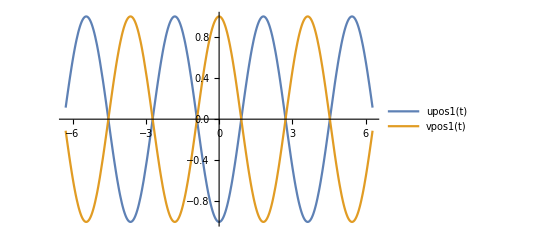

```mathematica
(*7a*)
Plot[{upos1[t],vpos1[t]},{t,-2*Pi,2*Pi},PlotLegends->"Expressions"]
```

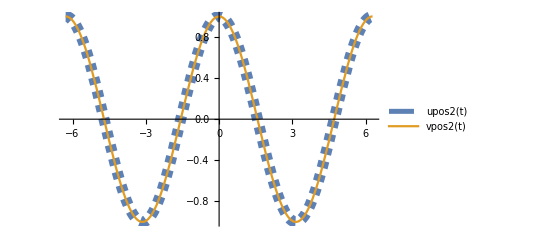

```mathematica
(*7b*)
Plot[{upos2[t],vpos2[t]},{t,-2*Pi,2*Pi},PlotStyle->{{Thickness[0.02],Dashed},{Thick}}, PlotLegends->"Expressions"]
```

### Problem 8. Coupled harmonic oscillators, general solution

If you shook this oscillator to get it moving it probably would NOT oscillate in a normal mode.  So what good are they?  The normal modes of oscillation are important because they serve as “basis functions” from which you can build ANY general oscillation.  As a simple example, let’s construct an oscillation by adding together equal amounts of the two normal modes - so the oscillation will be 1/2 mode 1 + 1/2 mode 2.  Then for example the position of mass 1 will be 1/2 upos1[t]+1/2 upos2[t].  
a) Make a plot of the two masses undergoing this type of vibration
b) Does the oscillation pattern repeat itself?  Do the two masses have the same oscillation frequencies?

```mathematica
(*8a*)
unew1[t_]=(1/2)upos1[t]+(1/2)upos2[t]
vnew1[t_]=(1/2)vpos1[t]+(1/2)vpos2[t]
```

Cos[t]/2-1/2 Cos[√3 t]

Cos[t]/2+1/2 Cos[√3 t]

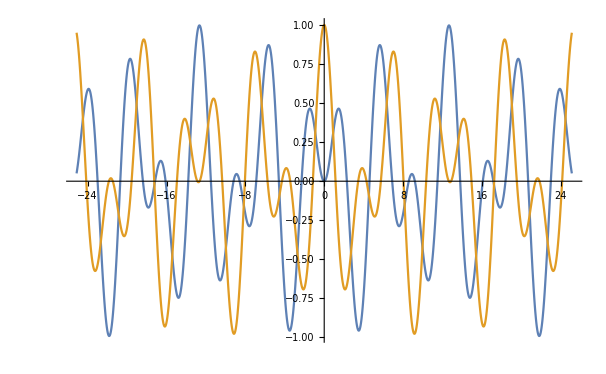

```mathematica
Plot[{unew1[t],vnew1[t]},{t,-8*Pi,8*Pi}]
```

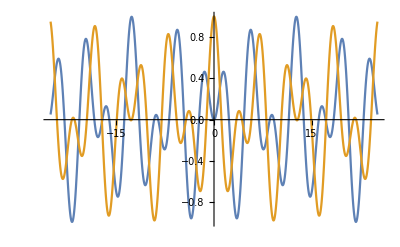
```mathematica
-Graphics-
(*8b*)
Yes, the oscillation pattern does repeat itself. The masses do have the same oscillation frequencies. This is clear since the two waves have the same period, thus the reciprocal of this period (the frequency) must also be the same.
```

```mathematica
x0=1.5 (* equilib positions of the masses are at ±x0 *);
xwall=3.5 (* wall positions are at ±xwall *);
wallgraphics={Thick,Black,Line[{{-xwall,-.5},{-xwall,.5}}],Line[{{xwall,-.5},{xwall,.5}}],Thin,Line[{{-x0,-.1},{-x0,.1}}],Line[{{x0,-.1},{x0,.1}}]};
```

Nothing to see if you just call it:

```mathematica
wallgraphics
```

{Thickness[Large],GrayLevel[0],Line[{{-3.5,-0.5},{-3.5,0.5}}],Line[{{3.5,-0.5},{3.5,0.5}}],Thickness[Tiny],Line[{{-1.5,-0.1},{-1.5,0.1}}],Line[{{1.5,-0.1},{1.5,0.1}}]}

### Problem 9. Coupled harmonic oscillators, animation

a) Modify the animation above to include the second oscillating mass and the other two springs.  Give them all different colors.  Mathematica recognizes color names such as Blue, Yellow, Red, Green, Magenta, Brown, Black, White, and others.  Mathematica draws the object in the order you list them, so you may have to play around with the order in which you call them to get them placed properly in front of or behind other objects.

b) When you have finished (a), copy & paste the animation command to another line, then modify it so that it shows the second normal mode.

```mathematica
Animate[Graphics[{Thick,Magenta,Line[{{-x0+upos1[t],0},{x0+upos1[t],0}}],Blue,Ball[{-x0+upos1[t],0},.15],Line[{{-xwall,0},{-x0+upos1[t],0}}],Green,Line[{{xwall,0},{x0+upos1[t],0}}],Ball[{x0+upos1[t],0},.15]},PlotRange->{{-xwall,xwall},{-1,1}}],{t,0,50},AnimationRate->2]
```

```mathematica
Animate[Graphics[{Thick,Magenta,Line[{{-x0+upos2[t],0},{x0+upos2[t],0}}],Blue,Ball[{-x0+upos2[t],0},.15],Line[{{-xwall,0},{-x0+upos2[t],0}}],Green,Line[{{xwall,0},{x0+upos2[t],0}}],Ball[{x0+upos2[t],0},.15]},PlotRange->{{-xwall,xwall},{-1,1}}],{t,0,50},AnimationRate->2]
```

What to turn in
When you are done, SAVE this entire file, with all your work.  Then SAVE it again under the new name “HW#10-yourname”, where yourname is of course, your name.  Delete all but the Assignments themselves (of which there are 9).  Make sure the entire worksheet runs correctly and that you haven’t deleted anything important!  Turn in this assignment worksheet, with all of its input and output code, through the link on our Moodle page.